# Night 4 Part 2

## 5

```mathematica
D[(x^2)*Sin[x*y^2], x]
```

x^2 y^2 Cos[x y^2]+2 x Sin[x y^2]

```mathematica
D[(x^2)*Sin[x*y^2], y]
```

2 x^3 y Cos[x y^2]

## 6

d^2f/dx^2

```mathematica
D[D[(x^2)*Sin[x*y^2], x], x]
```

4 x y^2 Cos[x y^2]+2 Sin[x y^2]-x^2 y^4 Sin[x y^2]

d^2f/dy^2

```mathematica
D[D[(x^2)*Sin[x*y^2], y], y]
```

2 x^3 Cos[x y^2]-4 x^4 y^2 Sin[x y^2]

d^f/dydx

```mathematica
D[D[(x^2)*Sin[x*y^2], y], x]
```

6 x^2 y Cos[x y^2]-2 x^3 y^3 Sin[x y^2]

d^f/dxdy

```mathematica
D[D[(x^2)*Sin[x*y^2], x], y]
```

6 x^2 y Cos[x y^2]-2 x^3 y^3 Sin[x y^2]

## 9a

```mathematica
Clear[x, y, z]
ContourPlot3D[x+ y+ z- 1 == 0, {x,0,1},{y,0,1},{z,0,1},PlotTheme->"Scientific", Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
RegionPlot3D[x+ y+ z- 1 <0,{x,0,1},{y,0,1},{z,0,1}, Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[1-x-y, {y, 0,1-x}],{x, 0, 1}]
```

1/6

## 9b

```mathematica
Clear[z]
```

```mathematica
ContourPlot3D[x^2+ y^2 == z, {x,-2,2},{y,-2,2},{z,0,2},PlotTheme->"Scientific", Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
RegionPlot3D[z≤(x^2)+(y^2)&&y≥(x^2)&&x≥(y^2), {x, -0.5, 1.5},{y, -0.5, 1.5},{z, -2, 2}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

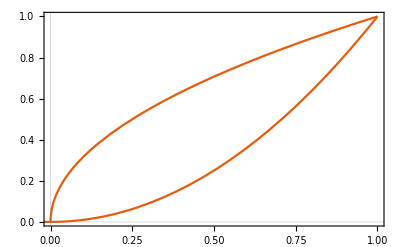

```mathematica
Show[Plot[x^2, {x,-1,1},PlotRange->{{0,1},{0,1}}, PlotTheme->"Scientific"], Plot[Sqrt[x], {x,-1,1},PlotRange->{{0,1},{0,1}}, PlotTheme->"Scientific"]]
```

```mathematica
Integrate[Integrate[(x^2)+(y^2), {y, x^2,Sqrt[x]}],{x, 0, 1}]
```

6/35

```mathematica
N[%]
```

0.171429

## 10a

Visualize and evaluate

```mathematica
RegionPlot3D[0≤z≤1&&0≤y≤(x+z)&&0≤x≤z, {x, 0, 1},{y, 0, 1},{z, 0, 1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[Integrate[1, {y, 0,x+z}],{x, 0, z}],{z, 0, 1}]
```

1/2

## 10b

```mathematica
RegionPlot3D[0≤x≤Sqrt[1-(z^2)]&&0≤z≤1&&0≤y≤(3), {x, 0, 1},{y, 0, 3},{z, 0, 1}, PlotPoints->60,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[Integrate[1, {x, 0,Sqrt[1-z^2]}],{z, 0, 1}],{y, 0, 3}]
```

(3 π)/4

## 11a

Visualize and figure out another triple integral that is the same

```mathematica
RegionPlot3D[0≤z≤(y)&&y≤x≤1&&0≤y≤(1), {x, 0, 1},{y, 0, 1},{z, 0, 1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

## 11b

```mathematica
RegionPlot3D[0≤x≤(1)&&0≤z≤(1-x^2)&&0≤y≤(1-x), {x, 0, 1},{y, 0, 1},{z, 0, 1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

## 12a

Visualize and evaluate

```mathematica
RegionPlot3D[0≤z≤(y)&&x≤y≤(2*x)&&0≤x≤(1), {x, 0, 1},{y, 0, 1},{z, 0, 1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[Integrate[2*x*y*z, {z, 0,y}],{y, x, 2*x}],{x, 0, 1}]
```

5/8

## 12b

```mathematica
RegionPlot3D[0≤x≤(y)&&0≤y≤(z)&&0≤z≤(1), {x, 0, 1},{y, 0, 1},{z, 0, 1}, PlotPoints->100,  Axes->True, AxesLabel->{x, y, z}]
```

-Graphics3D-

```mathematica
Integrate[Integrate[Integrate[z*Exp[-y^2], {x, 0,y}],{y, 0, z}],{z, 0, 1}]
```

1/(4 ⅇ)